## Test

### LLP Data:

```mathematica
effCodex = {{0,0.015619095400616526,0.00312572908148658},{0.25,0.023008739674361317,0.004324177839111181},{0.5,0.03151356619277295,0.005044286349414997},{0.75,0.03906858162918202,0.004886316425512489},{1,0.042320491502750295,0.003924438360978424},{1.25,0.03944614097858149,0.002610689507752481},{1.5,0.03196847336560891,0.0014305786869048672},{1.75,0.023108094531968913,0.0006586407166234164},{2,0.015356659002343596,0.00026522821016396956},{2.25,0.00964640121715529,0.0000973094955168887},{2.5,0.005836442121101962,0.000033614580336759165},{3,0.0019916324174676266,3.64444798458049*^-6},{3.5,0.0006473442067536317,3.7413079614232616*^-7},{4,0.00020658143393875516,3.772733646144437*^-8},{4.5,0.00006551823296669368,3.782752905501964*^-9},{7,2.0746811864136294*^-7,3.7873896758157997*^-14}};
```

```mathematica
effMat = {{0,0.011399089716925834,0.0009101702906910314},{0.25,0.021442577051561027,0.0026313045384514476},{0.5,0.03663935956249046,0.006196913794619277},{0.75,0.05688474781203432,0.012155703481024422},{1,0.08071801668500302,0.01950298671424161},{1.25,0.10546976334751318,0.025617175330058764},{1.5,0.12510751120796873,0.028139887556790845},{1.75,0.13252753246159407,0.025859220638954274},{2,0.12399261376267001,0.019500325121142456},{2.25,0.10227199353896393,0.011913501329914145},{2.5,0.07532136747038312,0.005985828116947375},{3,0.031982501239435274,0.000982837967334109},{3.5,0.011349355318271453,0.00011822070104888564},{4,0.003739158531928988,0.000012593769640498025},{4.5,0.0011986304365748342,1.2856552545727564*^-6},{7,3.814720479797806*^-6,1.2981093014683576*^-11}};
```

```mathematica
effAlex ={{0,0.5249045614028843,0.37985246509851717},{0.25,0.575059880936349,0.41282496436769783},{0.5,0.6012411763183173,0.41822646973460326},{0.75,0.5936573355652607,0.38611310744167676},{1,0.5473229841624935,0.3150653171653601},{1.25,0.465296592206761,0.21953990501729193},{1.5,0.3612185012970108,0.12771040415447757},{1.75,0.2562534458373926,0.062283342338100664},{2,0.16830525306538288,0.0262118029375411},{2.25,0.10435326464642876,0.00990240024118375},{2.5,0.062237538385598305,0.0034826797732596146},{3,0.02077936517368697,0.0003839439619047618},{3.5,0.006688466007358962,0.000039630527416614795},{4,0.0021270830915171494,4.003315804435735*^-6},{4.5,0.0006738515553045347,4.0161686101413255*^-7},{7,2.1326723194312613*^-6,4.022125060371749*^-12}};

effCodex2 ={{0,0.01908521212561322,0.00366897212224883},{0.25,0.028038153681031817,0.005567143981185686},{0.5,0.03823846568425234,0.006670572787786237},{0.75,0.04775758380363242,0.006672504530925624},{1,0.05253197757834629,0.005583325454185301},{1.25,0.04976631547037481,0.0037977205707761456},{1.5,0.04073192681257311,0.002093420657026131},{1.75,0.029528778914077188,0.0009621409593071818},{2,0.019573578403242295,0.00038535506639953755},{2.25,0.012196280905455693,0.00014055207596335107},{2.5,0.007296566938478131,0.00004832612597982955},{3,0.0024438175611126555,5.212631223705226*^-6},{3.5,0.0007874987391929169,5.34125699355054*^-7},{4,0.00025053490252520736,5.382829931210203*^-8},{4.5,0.00007937786978492012,5.396067992207895*^-9},{7,2.512367444507113*^-7,5.402138717181693*^-14}};
effMat2={{0,0.013973480167770948,0.0014986718619277013},{0.25,0.02486521709571254,0.003997825080639162},{0.5,0.03895020946257232,0.008246828102874047},{0.75,0.05685592790734548,0.01391081928424496},{1,0.07883525338858874,0.02029122637375282},{1.25,0.1026298690720048,0.02578744343365888},{1.5,0.1231442823418787,0.02811089197686701},{1.75,0.1327312682932221,0.025889944288487392},{2,0.12607241919258466,0.019745709514546878},{2.25,0.1054715449341591,0.012309707873770706},{2.5,0.07877014715148216,0.0063405767219066895},{3,0.03410165549492211,0.001086866908726942},{3.5,0.012159128206704624,0.0001333226004999127},{4,0.00400563101058087,0.000014288609047396518},{4.5,0.0012836204684650151,1.4612750396030344*^-6},{7,4.084318167857038*^-6,1.4765952692917632*^-11}}
effAlex2 = {{0,0.5506896544826301,0.3904971879295754},{0.25,0.608235760830053,0.42787026951233803},{0.5,0.6372639223256011,0.43564611657782093},{0.75,0.6285786818547799,0.40181868958836936},{1,0.5778706359173233,0.3250417907474602},{1.25,0.4885327914837358,0.22330712003249437},{1.5,0.3764546331605017,0.12825842052125527},{1.75,0.2653239196632627,0.062127046094641133},{2,0.17351523101502442,0.026098093478384817},{2.25,0.10732357268801784,0.009863138201640467},{2.5,0.06392687537627352,0.0034718839403330656},{3,0.021321170357279238,0.0003832324841688746},{3.5,0.006860760730376042,0.00003957696896503055},{4,0.002181671277069578,3.998586668907152*^-6},{4.5,0.0006911244954938324,4.01164509693948*^-7},{7,2.187309799407955*^-6,4.017699247006633*^-12}};
```

{{0,0.0139735,0.00149867},{0.25,0.0248652,0.00399783},{0.5,0.0389502,0.00824683},{0.75,0.0568559,0.0139108},{1,0.0788353,0.0202912},{1.25,0.10263,0.0257874},{1.5,0.123144,0.0281109},{1.75,0.132731,0.0258899},{2,0.126072,0.0197457},{2.25,0.105472,0.0123097},{2.5,0.0787701,0.00634058},{3,0.0341017,0.00108687},{3.5,0.0121591,0.000133323},{4,0.00400563,0.0000142886},{4.5,0.00128362,1.46128×10^-6},{7,4.08432×10^-6,1.4766×10^-11}}

```mathematica
SetDirectory[NotebookDirectory[]<>"/EJData"]
al3x1100 =Import["AL3X/alex_efflist_1100.txt","Table"];
al3x4100 =Import["AL3X/alex_efflist_4100.txt","Table"];
al3x8100 =Import["AL3X/alex_efflist_8100.txt","Table"];

al3x1150 =Import["AL3X/alex_efflist_1150.txt","Table"];
al3x4150 =Import["AL3X/alex_efflist_4150.txt","Table"];
al3x8150 =Import["AL3X/alex_efflist_8150.txt","Table"];

codex1100 =Import["CODEXb/codex_efflist_1100.txt","Table"];
codex4100 =Import["CODEXb/codex_efflist_4100.txt","Table"];
codex8100 =Import["CODEXb/codex_efflist_8100.txt","Table"];

codex1150 =Import["CODEXb/codex_efflist_1150.txt","Table"];
codex4150 =Import["CODEXb/codex_efflist_4150.txt","Table"];
codex8150 =Import["CODEXb/codex_efflist_8150.txt","Table"];

anubis1100 =Import["ANUBIS/anubis_efflist_1100.txt","Table"];anubis4100 =Import["ANUBIS/anubis_efflist_4100.txt","Table"];anubis8100 =Import["ANUBIS/anubis_efflist_8100.txt","Table"];

anubis1150 =Import["ANUBIS/anubis_efflist_1150.txt","Table"];anubis4150 =Import["ANUBIS/anubis_efflist_4150.txt","Table"];anubis8150 =Import["ANUBIS/anubis_efflist_8150.txt","Table"];

mat1100 =Import["MATHUSLA/mat_efflist_1100.txt","Table"];mat4100 =Import["MATHUSLA/mat_efflist_4100.txt","Table"];mat8100 =Import["MATHUSLA/mat_efflist_8100.txt","Table"];

mat1150 =Import["MATHUSLA/mat_efflist_1150.txt","Table"];mat4150 =Import["MATHUSLA/mat_efflist_4150.txt","Table"];mat8150 =Import["MATHUSLA/mat_efflist_8150.txt","Table"];

mapp1100 =Import["MAPP/mapp_efflist_1100.txt","Table"];mapp4100 =Import["MAPP/mapp_efflist_4100.txt","Table"];mapp8100 =Import["MAPP/mapp_efflist_8100.txt","Table"];

mapp1150 =Import["MAPP/mapp_efflist_1150.txt","Table"];mapp4150 =Import["MAPP/mapp_efflist_4150.txt","Table"];mapp8150 =Import["MAPP/mapp_efflist_8150.txt","Table"];

fas1100 =Import["FASER/pair-production/faser_efflist_1100.txt","Table"];fas4100 =Import["FASER/pair-production/faser_efflist_4100.txt","Table"];fas8100 =Import["FASER/pair-production/faser_efflist_8100.txt","Table"];

fas1100t =Import["FASER/t-channel/faser_efflist_tc_1100.txt","Table"];fas4100t =Import["FASER/t-channel/faser_efflist_tc_4100.txt","Table"];fas8100t =Import["FASER/t-channel/faser_efflist_tc_8100.txt","Table"];

for1100t =Import["FORMOSA/t-channel/for_efflist_tc_1100.txt","Table"];for4100t =Import["FORMOSA/t-channel/for_efflist_tc_4100.txt","Table"];for8100t =Import["FORMOSA/t-channel/for_efflist_tc_8100.txt","Table"];
```

/Users/dylanlinthorne/Dropbox/New Detectors/EJData

### Plotting:

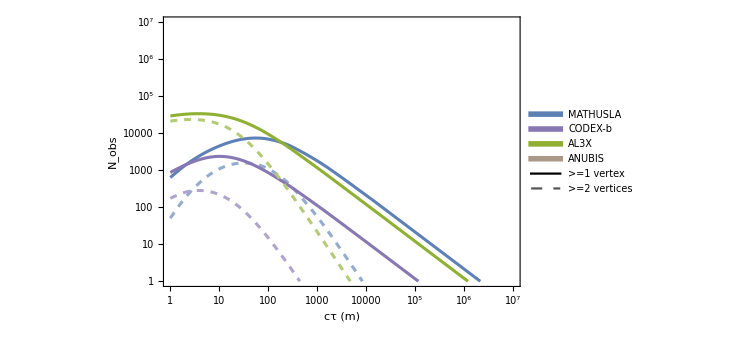

```mathematica
LLPxsecfb[11000]=3*6.2; 
LLPxsecfb[11500]=3*0.25;
Lumiifb=3000;
Lumiifc = 300;
Lumiifd = 250;


leg=LineLegend[{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.04]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.04]],
Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.04]],
Directive[Darker[LightOrange],Thickness[0.04]],Directive[Black],Directive[Lighter[Black],Dashed]},{"MATHUSLA","CODEX-b","AL3X","ANUBIS", ">=1 vertex",">=2 vertices"}];

legfas=LineLegend[{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.04]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.04]],
Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.04]],
Directive[Black],Directive[Lighter[Black],Dashed]},
{"m = 1","m = 4","m = 8", "t-channel","X-production"}];

ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@effMat,{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@effMat, {10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@effCodex,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@effCodex,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@effAlex,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@effAlex},
Joined->True,
InterpolationOrder->2,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["LLP Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
ImageSize->550,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{1,10^7},{1,10^7}},
Epilog->Inset[leg,{12.8,12}]
]
```

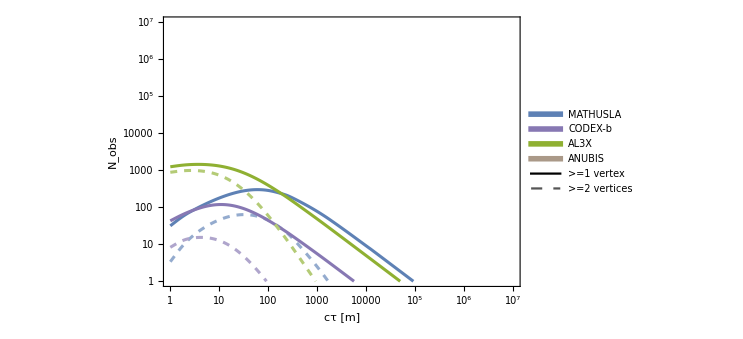

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[2]]}&/@effMat2,{10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[3]]}&/@effMat2, {10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[2]]}&/@effCodex2,
{10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[3]]}&/@effCodex2,
{10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[2]]}&/@effAlex2,
{10^#[[1]],Lumiifb*LLPxsecfb[11500]*#[[3]]}&/@effAlex2},
Joined->True,
InterpolationOrder->2,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ [m]",22],Style[StringJoin["LLP Detector Projections, M_X = 1.5 TeV"],20]}},
FrameStyle->15,
ImageSize->550,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{1,10^7},{1,10^7}},
Epilog->Inset[leg,{12.8,12}]
]
```

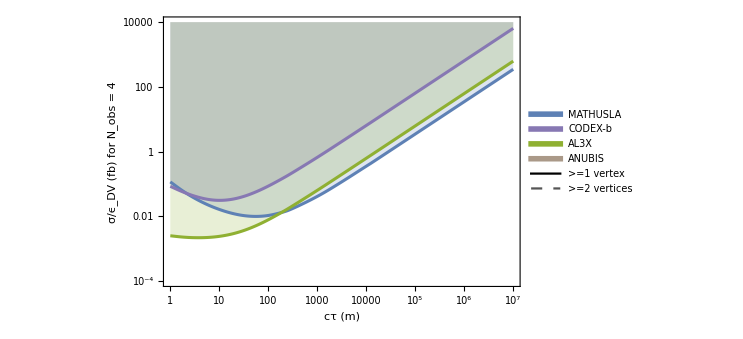

```mathematica
leg2=LineLegend[{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.04]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.04]],
Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.04]],Directive[Black],Directive[Lighter[Black],Dashed]},{"MATHUSLA","CODEX-b","AL3X", ">=1 vertex",">=2 vertices"}];

ListLogLogPlot[{{10^#[[1]],4/(Lumiifb*#[[2]])}&/@effMat,{10^#[[1]],4/(Lumiifb*#[[2]])}&/@effCodex,{10^#[[1]],4/(Lumiifb*#[[2]])}&/@effAlex},
Joined->True,
InterpolationOrder->2,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["σ/ϵ_DV (fb) for N_obs = 4",22],},{Style["cτ (m)",22],Style[StringJoin["LLP Limit On Cross Section, M_X = 1 TeV"],20]}},
FrameStyle->15,
ImageSize->550,
Filling->Top,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]]},
PlotRange->{{1,10^7},{10^-4,10^4}},
Epilog->Inset[leg,{13.8,Log[.0003]}]
]
```

{{1/10,0.200064},{0.177828,0.272932},{0.316228,0.342622},{0.562341,0.409324},{1,0.467996},{1.77828,0.506074},{3.16228,0.511083},{5.62341,0.476477},{10,0.40509},{17.7828,0.311901},{31.6228,0.218804},{56.2341,0.14231},{100,0.0876343},{177.828,0.0520437},{316.228,0.0302162},{1000,0.00983515},{3162.28,0.00313921},{10000,0.000995645},{31622.8,0.000315146},{10000000,9.9701×10^-7}}

{{1,0.00091017},{1.77828,0.0026313},{3.16228,0.00619691},{5.62341,0.0121557},{10,0.019503},{17.7828,0.0256172},{31.6228,0.0281399},{56.2341,0.0258592},{100,0.0195003},{177.828,0.0119135},{316.228,0.00598583},{1000,0.000982838},{3162.28,0.000118221},{10000,0.0000125938},{31622.8,1.28566×10^-6},{10000000,1.29811×10^-11}}

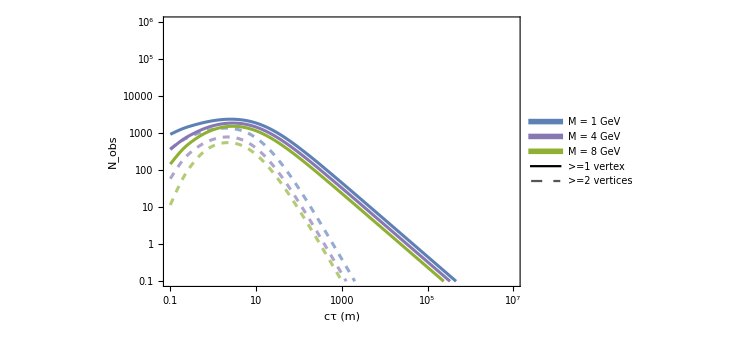

ListLogLogPlot::ioproc: {{-2.30259, Log[1.45297\\\ Lumiifd]}, {-1.72694, Log[2.47763\\\ Lumiifd]}, {-1.15129, Log[3.70827\\\ Lumiifd]}, {-0.575646, Log[5.07672\\\ Lumiifd]}, «3», {1.72694, Log[6.99184\\\ Lumiifd]}, {2.30259, Log[5.85654\\\ Lumiifd]}, {2.87823, Log[4.41846\\\ Lumiifd]}, «10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogLogPlot::ioproc will be suppressed during this calculation.

```mathematica
leg3=LineLegend[{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.04]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.04]],
Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.04]],Directive[Black],Directive[Lighter[Black],Dashed]},{"M = 1 GeV","M = 4 GeV","M = 8 GeV", ">=1 vertex",">=2 vertices"}];

{10^#[[1]],#[[2]]}&/@al3x1100
{10^#[[1]],#[[3]]}&/@effMat
ListLogLogPlot[{{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[2]]}&/@al3x1100,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[3]]}&/@al3x1150,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[2]]}&/@al3x4100,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[3]]}&/@al3x4150,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[2]]}&/@al3x8100,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[3]]}&/@al3x8150},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["AL3X Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{0.1,10^6}},
ImageSize->550,
Epilog->Inset[leg3,{12.8,10}]
]
```

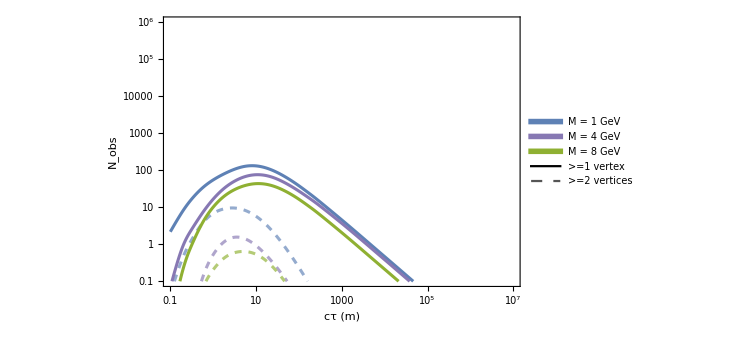

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[2]]}&/@codex1100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[3]]}&/@codex1100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[2]]}&/@codex4100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[3]]}&/@codex4100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[2]]}&/@codex8100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[3]]}&/@codex8100},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["CODEXb Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{0.1,10^6}},
ImageSize->550,
Epilog->Inset[leg3,{12.8,10}]
]
```

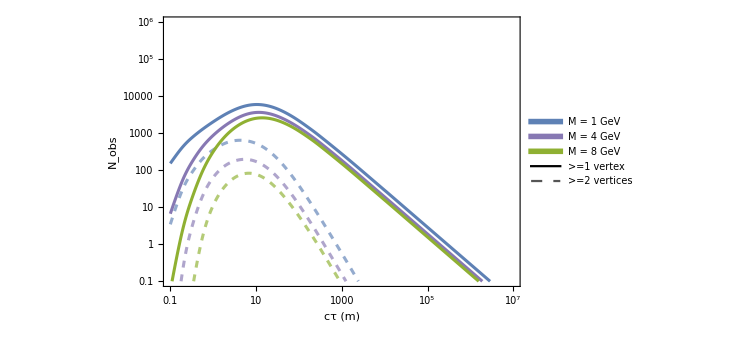

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@anubis1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@anubis1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@anubis4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@anubis4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@anubis8100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@anubis8100},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["ANUBIS Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{0.1,10^6}},
ImageSize->550,
Epilog->Inset[leg3,{12.8,10}]
]
```

ListLogLogPlot::ioproc: {{-2.30259,Indeterminate},{-1.72694,-47.3028},{-1.15129,-25.6241},{-0.575646,-13.0745},{0.,-5.9359},{0.575646,-1.81916},{1.15129,0.578437},{1.72694,2.05817},{2.30259,3.071},{2.87823,3.74557},«10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

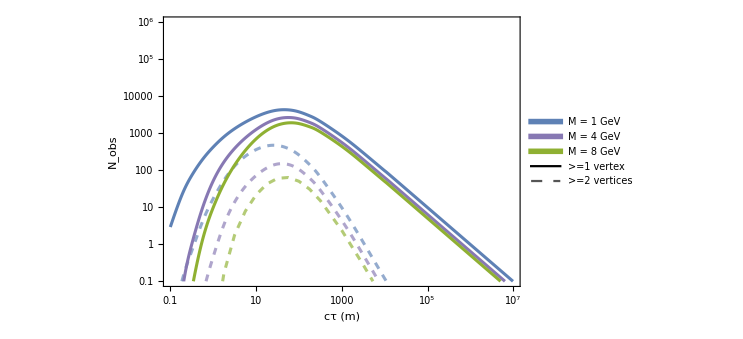

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mat1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mat1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mat4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mat4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mat8100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mat8100},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["MATHUSLA Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{0.1,10^6}},
ImageSize->550,
Epilog->Inset[leg3,{12.8,10}]
]
```

ListLogLogPlot::ioproc: {{-2.30259,Indeterminate},{-1.72694,Indeterminate},{-1.15129,Indeterminate},{-0.575646,Indeterminate},{0.,Indeterminate},{0.575646,Indeterminate},{1.15129,Indeterminate},{1.72694,Indeterminate},{2.30259,Indeterminate},{2.87823,Indeterminate},«10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

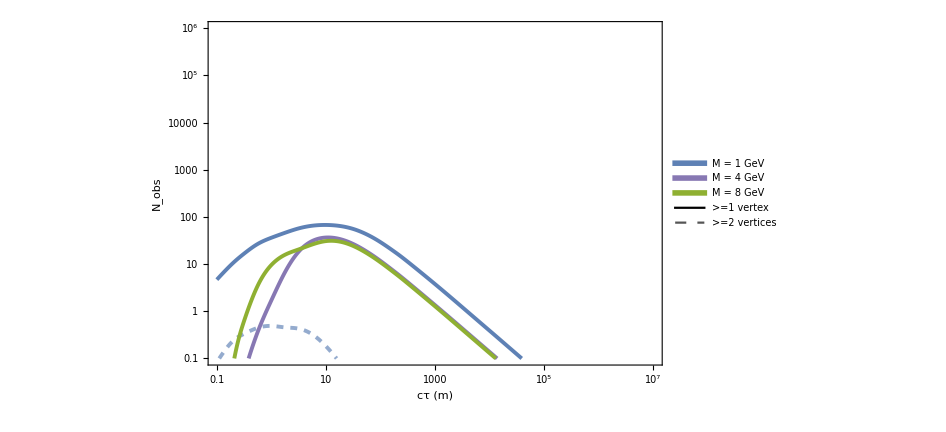

```mathematica
(*ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mapp1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mapp1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mapp4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mapp4100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mapp8100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mapp8100},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["MAPP Detector Projections, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{0.1,10^6}},
ImageSize->700,
Epilog->Inset[leg3,{12.8,10}]
]*)
```

ListLogLogPlot::ioproc: {{-2.30259,Indeterminate},{-1.72694,-27.6642},{-1.15129,-16.876},{-0.575646,-10.9045},{0.,-7.60973},{0.575646,-5.87841},{1.15129,-5.0499},{1.72694,-4.75262},{2.30259,-4.79343},{2.87823,-5.05081},«10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogLogPlot::ioproc: {{-2.30259,Indeterminate},{-1.72694,Indeterminate},{-1.15129,Indeterminate},{-0.575646,Indeterminate},{0.,-26.7959},{0.575646,-17.5069},{1.15129,-12.5248},{1.72694,-9.89439},{2.30259,-8.44778},{2.87823,-7.62528},«10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogLogPlot::ioproc: {{-2.30259,Indeterminate},{-1.72694,Indeterminate},{-1.15129,Indeterminate},{-0.575646,Indeterminate},{0.,-30.8823},{0.575646,-19.7301},{1.15129,-13.7086},{1.72694,-10.5736},{2.30259,-9.05535},{2.87823,-8.36453},«10»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogLogPlot::ioproc will be suppressed during this calculation.

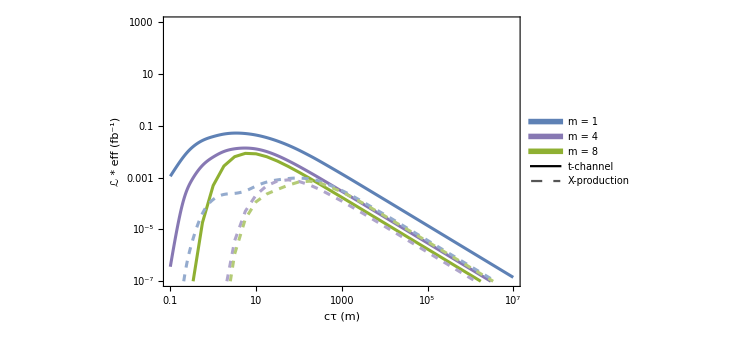

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifb*#[[2]]}&/@fas1100t,
{10^#[[1]],Lumiifb*#[[2]]}&/@fas4100t,
{10^#[[1]],Lumiifb*#[[2]]}&/@fas8100t,
{10^#[[1]],Lumiifb*#[[2]]}&/@fas1100,
{10^#[[1]],Lumiifb*#[[2]]}&/@fas4100,
{10^#[[1]],Lumiifb*#[[2]]}&/@fas8100
},
Joined->True,
InterpolationOrder->3,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["ℒ * eff (fb^-1)",22],},{Style["cτ (m)",22],Style[StringJoin["FASER Detector Efficiencies, M_X = 1 TeV"],20]}},
FrameStyle->15,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],
Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],
Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],
Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed]
},
PlotRange->{{.1,10^7},{0.0000001,10^3}},
ImageSize->550,
Epilog->Inset[legfas,{Log[100000],Log[1]}]
]
```

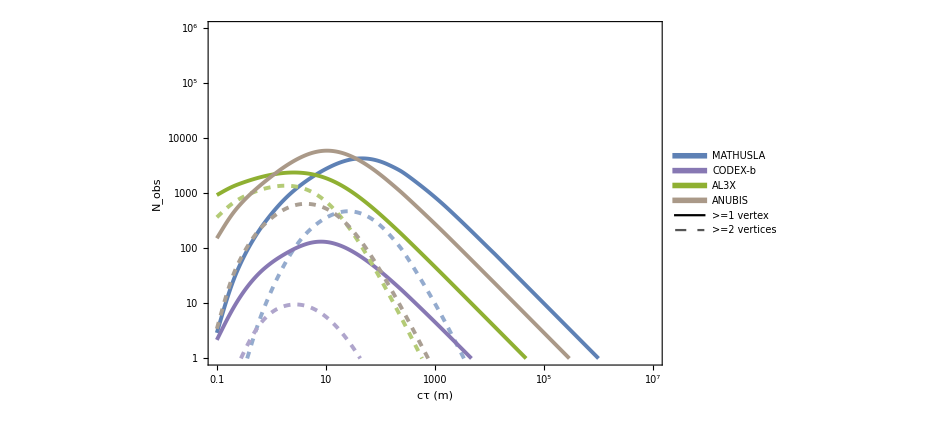

```mathematica
ListLogLogPlot[{{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@mat1100,{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@mat1100, {10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[2]]}&/@codex1100,
{10^#[[1]],Lumiifc*LLPxsecfb[11000]*#[[3]]}&/@codex1100,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[2]]}&/@al3x1100,
{10^#[[1]],Lumiifd*LLPxsecfb[11000]*#[[3]]}&/@al3x1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[2]]}&/@anubis1100,
{10^#[[1]],Lumiifb*LLPxsecfb[11000]*#[[3]]}&/@anubis1100}
,
Joined->True,
InterpolationOrder->2,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["N_obs",22],},{Style["cτ (m)",22],Style[StringJoin["LLP Detector Projections: M_X = 1 TeV, M_pi = 1 GeV"],20]}},
FrameStyle->15,
ImageSize->700,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[Lighter[RGBColor[0.368417,0.506779,0.709798]],Thickness[0.004],Dashed],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[Lighter[RGBColor[0.528488,0.470624,0.701351]],Thickness[0.004],Dashed],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],Directive[Lighter[RGBColor[0.560181,0.691569,0.194885]],Thickness[0.004],Dashed],
Directive[Darker[LightOrange],Thickness[0.004]],Directive[Darker[Lighter[LightOrange]],Thickness[0.004],Dashed]},
PlotRange->{{.1,10^7},{1,10^6}},
Epilog->Inset[leg,{12.8,10}]
]
```

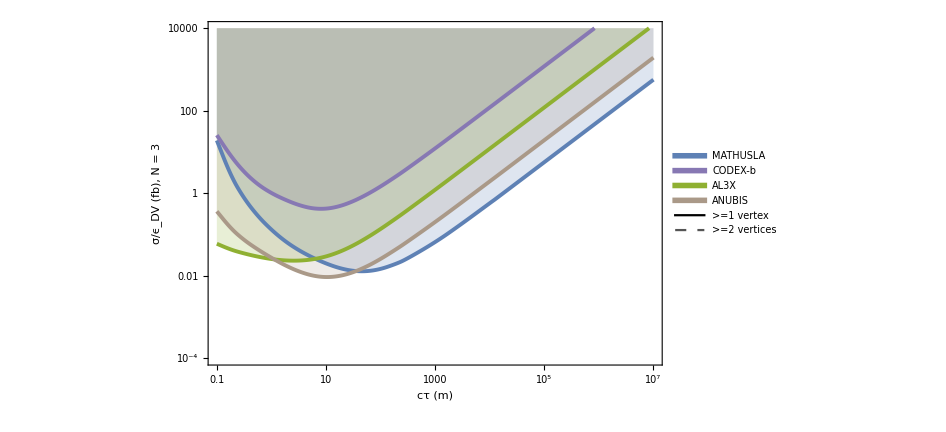

```mathematica
ListLogLogPlot[{{10^#[[1]],3/(Lumiifb*#[[2]])}&/@mat1100,{10^#[[1]],3/(Lumiifc*#[[2]])}&/@codex1100,{10^#[[1]],3/(Lumiifd*#[[2]])}&/@al3x1100, {10^#[[1]],3/(Lumiifb*#[[2]])}&/@anubis1100},
Joined->True,
InterpolationOrder->2,
Frame->True,
LabelStyle->{FontFamily->"Times New Roman", Black},
FrameLabel->{{Style["σ/ϵ_DV (fb), N = 3",22],},{Style["cτ (m)",22],Style[StringJoin["LLP Limit On Cross Section, M_X = 1 TeV"],20]}},
FrameStyle->15,
ImageSize->700,
Filling->Top,
PlotStyle->{Directive[RGBColor[0.368417,0.506779,0.709798],Thickness[0.004]],Directive[RGBColor[0.528488,0.470624,0.701351],Thickness[0.004]],Directive[RGBColor[0.560181,0.691569,0.194885],Thickness[0.004]],
Directive[Darker[LightOrange],Thickness[0.004]]},
PlotRange->{{.1,10^7},{10^-4,10^4}},
Epilog->Inset[leg,{13.8,Log[.0006]}]
]
```